```mathematica
xc = 0;
yc = 0;
ptc = {xc,yc};
ptmax = {xmax, ymax};
ri = 1;
kg = 2.1;
rg = ri *kg;
initialcircle = CirclePoints[ri, 1]
gradient= Grad[Sin[0.3x]Sin[0.5y],{x,y}]
gradient /. {x->{1,2},y->{1,2}}
```

{{0,1}}

{0.3 Cos[0.3 x] Sin[0.5 y],0.5 Cos[0.5 y] Sin[0.3 x]}

{{0.137404,0.208349},{0.129672,0.152539}}



```mathematica
p0 = Graphics[initialcircle]
```

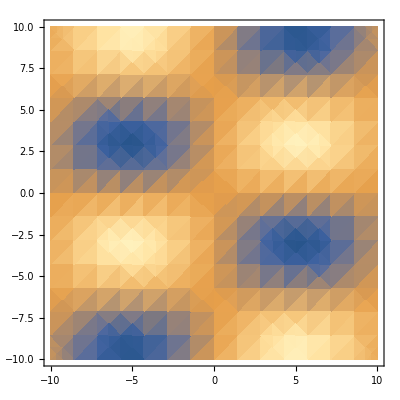

```mathematica
p1 = DensityPlot[Sin[0.3x]Sin[0.5y],{x,-10,10},{y,-10,10}]
```

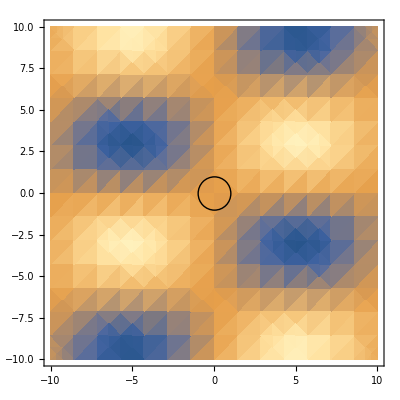

{}

```mathematica
Show[p1,p0]
```